Yohan Lee Lab 1

Problem 1

Define function f

```mathematica
f[x_]  := 1/(1+x^2)
```

```mathematica
Function[x,1/(1+x^2)]
```

Function[x,1/(1+x^2)]

Evaluate third derivative of f at x=2

```mathematica
f'''[2]
```

-144/625

Problem 2

Function 1 integrated over interval [0, 2]

```mathematica
Integrate[x^3*Exp[x],{x,0,2}]
```

2 (3+ⅇ^2)

Function 2 integrated over invertal [0, Pi]

```mathematica
Integrate[Sin[x], {x, 0, Pi}]
```

2

Problem 3

Graph both functions in separate plots

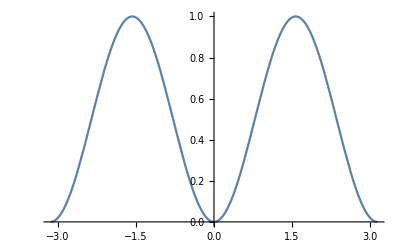

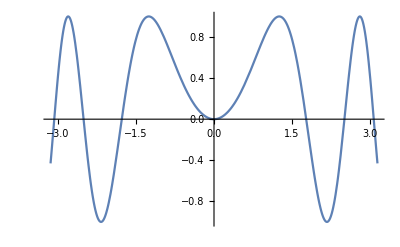

```mathematica
Plot[(Sin[x])^2, {x, -Pi, Pi}]
Plot[Sin[x^2], {x, -Pi, Pi}]
```

Problem 4

Graph both functions with axis labels

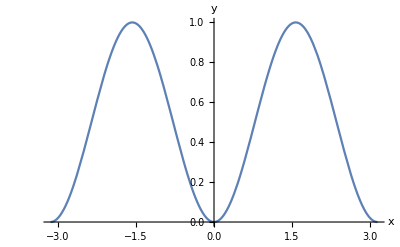

```mathematica
Plot[(Sin[x])^2, {x, -Pi, Pi}, AxesLabel->{x,y}]
```

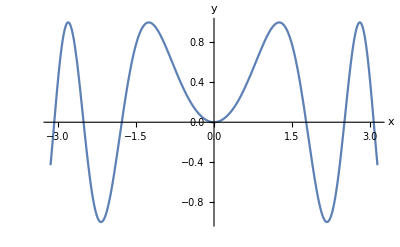

```mathematica
Plot[(Sin[x^2]), {x, -Pi, Pi}, AxesLabel->{x,y}]
```

Problem 5

Define function g

```mathematica
g[x_]:=1/(√(1-x^2))
```

```mathematica
Function[x,1/(√(1-x^2))]
```

Function[x,1/(√(1-x^2))]

Find value of derivative of g evaluated at x=1/2

```mathematica
Function[x,1/(√(1-x^2))]'
```

Function[x,x/(√(1-x^2) (√(1-x^2))^2)]

```mathematica
Function[x,x/(√(1-x^2) (√(1-x^2))^2)][1/2]
```

4/(3 √3)

Find antiderivative of g

```mathematica
Integrate[g[x],x]
```

ArcSin[x]

Compute integral of g on interval (0, 1)

```mathematica
Integrate[g[x], {x,0,1}]
```

π/2

Plot g on the interval (-1, 1)

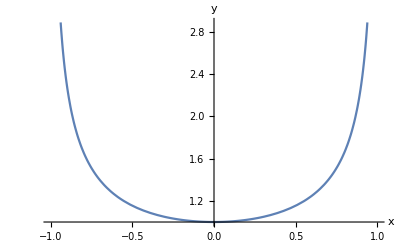

```mathematica
Plot[g[x], {x,-1,1}, AxesLabel->{x,y}]
```

Problem 6

Define function

```mathematica
Clear[f]
```

```mathematica
f[x_]:=(1-Tan[x])/(Sin[x]-Cos[x])
```

```mathematica
Function[x,(1-Tan[x])/(Sin[x]-Cos[x])]
```

Function[x,(1-Tan[x])/(Sin[x]-Cos[x])]

Compute limit as x->Pi/4

```mathematica
Limit[f[x],x->Pi/4]
```

-√2

Problem 7

Define function

```mathematica
Clear[f]
```

```mathematica
f[x_]:=Cos[x+1]+Log[x-1]+x*Exp[x^2+1]
```

```mathematica
Function[x,Cos[x+1]+Log[x-1]+x Exp[x^2+1]]
```

Function[x,Cos[x+1]+Log[x-1]+x Exp[x^2+1]]

Compute fourth derivative of f

```mathematica
f''''[x]
```

-6/(-1+x)^4+60 ⅇ^(1+x^2) x+80 ⅇ^(1+x^2) x^3+16 ⅇ^(1+x^2) x^5+Cos[1+x]

Compute integral of f on interval [2,4]

```mathematica
Integrate[f[x], {x,2,4}]
```

-2+1/2 ⅇ^5 (-1+ⅇ^12)+Log[27]-Sin[3]+Sin[5]

```mathematica
N[-2+1/2 ⅇ^5 (-1+ⅇ^12)+Log[27]-Sin[3]+Sin[5]]
```

1.20774×10^7